```mathematica
SetDirectory[NotebookDirectory[]];
hits = Import["hits.txt","Data"];
hitswithout = Import["hitswithout.txt","Data"];
```

```mathematica
hits=Flatten[hits];
angles={};
hitswithout=Flatten[hitswithout];
angleswithout={};
```

```mathematica
For[i=1,i≤Length[hits],i=i+5,
If[hits[[i+4]]=="e-" && hits[[i+9]]=="e+" && hits[[i+3]]==hits[[i+8]],
AppendTo[angles,(180/Pi)*ArcCos[hits[[i]]*hits[[i+5]]+hits[[i+1]]*hits[[i+6]]+hits[[i+2]]*hits[[i+7]]]]];]
For[i=1,i≤Length[hitswithout],i=i+5,
If[hitswithout[[i+4]]=="e-" && hitswithout[[i+9]]=="e+" && hitswithout[[i+3]]==hitswithout[[i+8]],
AppendTo[angleswithout,(180/Pi)*ArcCos[hitswithout[[i]]*hitswithout[[i+5]]+hitswithout[[i+1]]*hitswithout[[i+6]]+hitswithout[[i+2]]*hitswithout[[i+7]]]]];]
```

Part::partw: Part 3569525 of {-0.291064,-0.0721466,0.953979,67,e-,-0.230123,-0.124347,0.965185,511,e-,-0.216418,0.181956,-0.959195,548,e-,«22»,0.214663,1072,e+,-0.0685082,0.980022,0.186716,1072,e-,0.840475,0.243421,-0.484095,1082,e-,«3569470»} does not exist.

Part::partw: Part 3569524 of {-0.291064,-0.0721466,0.953979,67,e-,-0.230123,-0.124347,0.965185,511,e-,-0.216418,0.181956,-0.959195,548,e-,«22»,0.214663,1072,e+,-0.0685082,0.980022,0.186716,1072,e-,0.840475,0.243421,-0.484095,1082,e-,«3569470»} does not exist.

```mathematica
angles
```

{43.2698,27.4674,15.9106,1.29287,10.476,20.7863,9.85771,109177,83.7071,11.1717,13.7884,7.36007,95.2783,10.2746,113.245}
 |  |  |  |

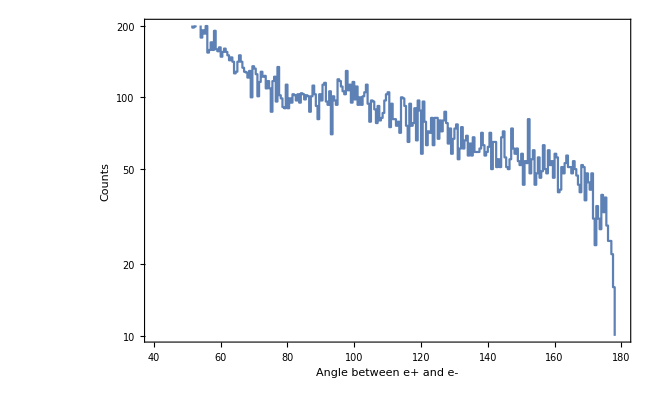

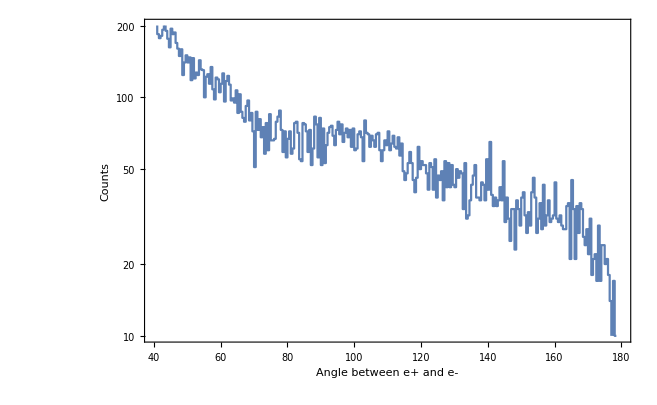

```mathematica
hist=HistogramList[angles,{.5}];

ListLogPlot[Transpose[{hist[[1]],ArrayPad[hist[[2]],{0,1},"Fixed"]}],InterpolationOrder->0,Joined->True,AxesOrigin->{0,0},PlotRange->{{40,180},{10,200}},RotateLabel->True,FrameLabel->{Style["Angle between e+ and e-",20,Bold,Blue],Style["Counts",20,Bold,Blue]},
LabelStyle->Directive[Blue,Bold],Frame->True]
histwithout=HistogramList[angleswithout,{.5}];

ListLogPlot[Transpose[{histwithout[[1]],ArrayPad[histwithout[[2]],{0,1},"Fixed"]}],InterpolationOrder->0,Joined->True,AxesOrigin->{0,0},PlotRange->{{40,180},{10,200}},RotateLabel->True,FrameLabel->{Style["Angle between e+ and e-",20,Bold,Blue],Style["Counts",20,Bold,Blue]},
LabelStyle->Directive[Blue,Bold],Frame->True]
```

```mathematica
Length[angles]
```

109191

```mathematica
180*ArcCos[-0.9087]/Pi
```

155.326